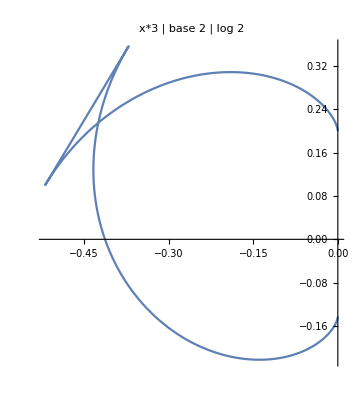

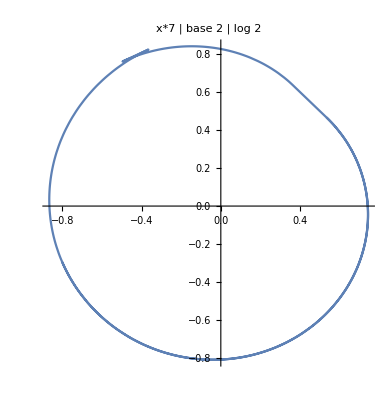

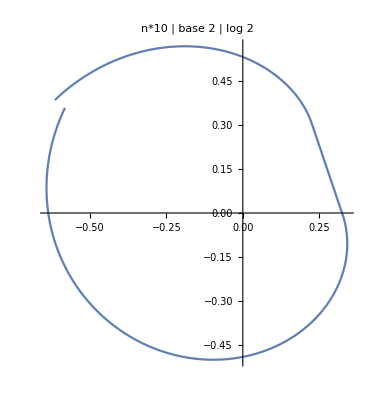

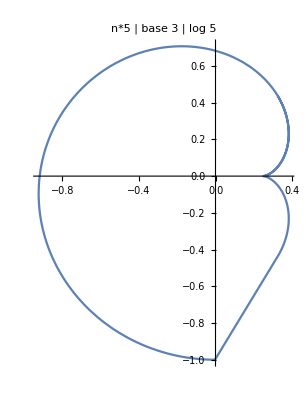

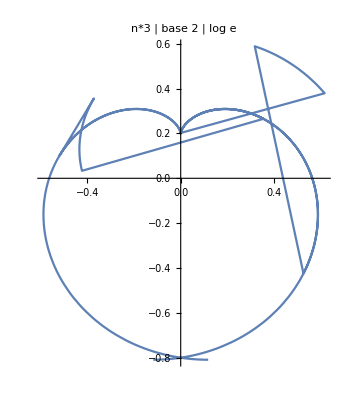

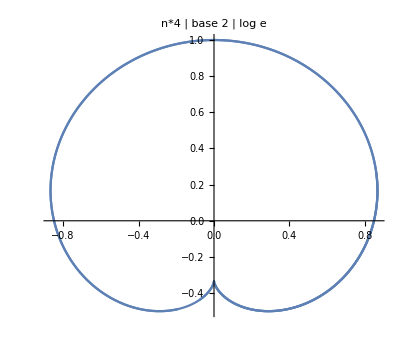

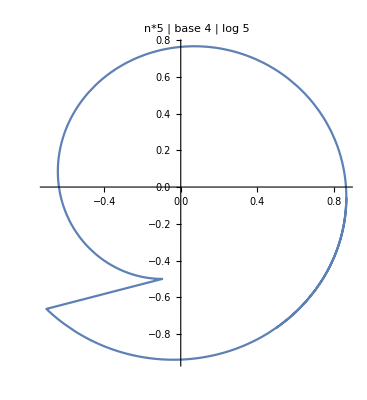

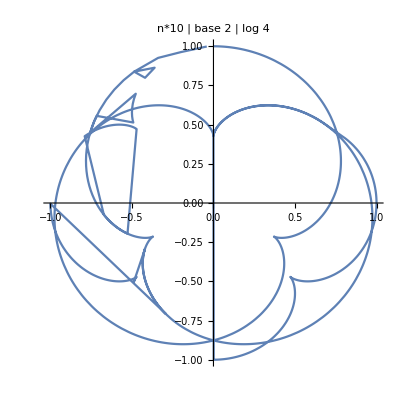

```mathematica
ClearAll["Global`*"]

F[x_,y_,t_,f_,g_]:=Sin[2*Pi*(g[f[t]]-g[t])]-y*(Sin[2*Pi*g[f[t]]]-Sin[2*Pi*g[t]])-x*(Cos[2*Pi*g[f[t]]]-Cos[2*Pi*g[t]]);

Fd[x_,y_,t_,f_,g_]:= 2 Pi( f'[t] g'[f[t]](Cos[2 Pi (g[f[t]]-g[t])]-y Cos[2 Pi g[f[t]]]+x Sin[2 Pi g[f[t]]])-g'[t](Cos[2 Pi (g[f[t]]-g[t])]-y Cos[2 Pi g[t]] +x Sin[2 Pi g[t]]) );

parametricFunc[t_,f_,g_]:={x,y}/.(Solve[F[x,y,t,f,g]==0&&Fd[x,y,t,f,g]==0,{x,y}]);

plot[f_,g_,from_,to_,label_]:=ParametricPlot[parametricFunc[t,f,g],{t,from,to},PlotLabel->label];

f[x_]:=x*3;
g[x_]:=x/2^Floor[Log[2,x]];
plot[f, g, 1,2,"x*3 | base 2 | log 2"]

f[x_]:=x*7;
g[x_]:=x/2^Floor[Log[2,x]];
plot[f, g, 0.7,2,"x*7 | base 2 | log 2"]

f[n_]:=n*10;
g[n_]:=n/2^Floor[Log[2,n]];
plot[f, g,1.05,2, "n*10 | base 2 | log 2"]

f[n_]:=n*5;
g[n_]:=n/(2*3^Floor[Log[5,n]]);
plot[f, g, 0.5,2,"n*5 | base 3 | log 5"]

f[n_]:=n*3;
g[n_]:=n/2^Floor[Log[n]];
plot[f, g, 0.05,0.8,"n*3 | base 2 | log e"]

f[n_]:=n*4;
g[n_]:=n/2^Floor[Log[n]];
plot[f, g, 0,2,"n*4 | base 2 | log e"]

f[n_]:=n*5;
g[n_]:=n/(3*4^Floor[Log[5,n]]);
plot[f, g, 0.4,2,"n*5 | base 4 | log 5"]

f[n_]:=n*10;
g[n_]:=n/2^Floor[Log[4,n]];
plot[f, g, 0,1,"n*10 | base 2 | log 4"]

f[n_]:=n*7;
g[n_]:=n/2^Floor[Log[n]];
plot[f, g, 1.4,2.5,"n*7 | base 2 | log n"]

f[n_]:=n^3;
g[n_]:=n/2^Floor[Log[2,n]];
plot[f, g, 1,2,"n^3 | base 2 | log 2"]

f[n_]:=2^n;
g[n_]:=n/(2*3^Floor[Log[3,n]]);
plot[f, g, 0,5,"2^n | base 3 | log 3"]

f[n_]:=2^n;
g[n_]:=n/(5*6^Floor[Log[6,n]]);
plot[f, g, 0,5,"2^n | base 3 | log 3"]
```